# Geometric structure of thermal cones

```mathematica
Clear["Global`*"]
```

#### This is a supplementary notebook of the manuscript “Geometric structure of thermal cones”. Here, we provide a code to construct the thermal cones for an energy-incoherent state p, with Hamiltonian H, interacting with a heat bath at inverse temperature β.

## Catalogue of functions

```mathematica
Clear["Global`*"]
```

All functions used to construct the thermal cones or obtain some of their properties are listed below. Almost all commands are illustrated in the Examples.

```mathematica
projection[x_]:=#⟦;;-2⟧/(2+#⟦-1⟧)&[(x )] (*Projects from dimension d to dimension d-1. Helper function for visualizing high-dimensional objects.*)
projection3D[x_]:=If[Length[x]>3,Nest[projection[#]&,x,Length[x]-3],x](*Projection from any dimension d to min(3,d)*)
simplexProj[d_]:=Reverse/@Table[Normalize[PadLeft[Flatten[{n,Table[-1,n]}],d]],{n,1,d-1}] (*Helper function for projecting d+1-dimensional probability distributions to d-dimensional simplex*)

funcFromPoints[points_]:=Interpolation[points,InterpolationOrder->1](*Given a set of (x-axis-ordered) points it creates a piecewise-linear function of x joining the points*)

γs[Es_,β_]:=Exp[-Es β]; (*γ coefficients based on the given inverse temperature β and energies*)
GibbsState[Es_,β_]:=Normalize[γs[Es,β],Total];  (*Gibbs state from normalized γ coefficients*)
βorder[p_,Es_,β_]:=Ordering[-p/γs[Es,β]]; (*Function generating a β-order given a probability distribution p, inverse temperature β and energies*)

ThermoMajorizationCurveElbows[p_,Es_,β_]:=Module[{opvec,oγs},
opvec=p⟦βorder[p,Es,β]⟧;
oγs=γs[Es,β]⟦βorder[p,Es,β]⟧;
Prepend[Accumulate[Transpose[{oγs,opvec}]],{0,0}]] (*Function generating the elbows of the thermomajorization curve of a probability distribution p, inverse temperature β and energies*)

ThermoMajorizationCurve[i_,ps_,Es_:{1,1,1},β_:0]:=funcFromPoints[ThermoMajorizationCurveElbows[ps,Es,β]] [i](*Function generating the thermomajorization curve of a probability distribution p, inverse temperature β and energies*)

FutureExtremePoints[p_,Es_,β_]:=
Table[Differences[Prepend[Table[ThermoMajorizationCurve[i,p,Es,β],{i,Accumulate[γs[Es,β]⟦j⟧]}],0]]⟦InversePermutation[j]⟧,{j,Permutations[Range[Length[p]]]}](*Function generating all Extreme points of the Future Thermal Cone by considering all possible β-orders and subsequently taking the corresponding points of the original thermomajorization curve.*)

FutureThermalConeRaw[p_,Es_,β_]:=ConvexHullMesh[projection3D[simplexProj[Length[p]].#]&/@FutureExtremePoints[p,Es,β]](*Function generates the future thermal cone as the convex hull of the extremal points.*)

FutureThermalCone[p_,Es_,β_]:= Module[{f = If[Length[p]>3,Graphics3D[#,Boxed->False,Method->{"ShrinkWrap" -> True}]&,Graphics[#]&]},f[{FaceForm[Opacity[0.45,RGBColor["#91FF85"]]],EdgeForm[{Thick,RGBColor["#437F3B"]}],FutureThermalConeRaw[p,Es,β]}]]
(*Graphical representation of the Future Thermal Cone*)

tvectors[p_,Es_,β_,perm_]:=Module[{γ,βO},
γ=γs[β,Es];
βO =βorder[p,β,Es];
Table[
Append[#,1-Total[#]]&[
Flatten[{
Sum[p⟦βO⟧⟦k⟧,{k,1,j-1}]-(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)(Sum[γ⟦βO⟧⟦k⟧,{k,1,j-1}]-γ⟦perm⟧⟦1⟧),
Table[(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)γ⟦perm⟧⟦k⟧,
{k,2,Length[p]-1}]}]]⟦InversePermutation[perm]⟧,
{j,1,Length[p]}]](*Function generates the tangent vectors for a given β-order [Eq.29 of "Geometric structure of thermal cones"]*)

Alltvectors[p_,Es_,β_]:=
Transpose[Table[tvectors[p,Es,β,perm],{perm,Permutations[Range[Length[p]]]}]] (*Function generates all tangent vectors*)

SetT[p_,Es_,β_]:=
RegionUnion[Table[RegionUnion[Table[ConvexHullMesh[simplexProj[Length[p]].#&/@
Union[FutureExtremePoints[tvectors[p,Es,β,k]⟦j⟧,Es,β],
FutureExtremePoints[tvectors[p,Es,β,k]⟦j+1⟧,Es,β]]],{j,1,2}]],{k,Permutations[Range[Length[p]]]}]] (*Function generates the set T [Eq.31 of "Geometric structure of thermal cones"] *)

IncomparableRegionRaw[p_,Es_,β_]:=Module[{t = Transpose[Alltvectors[p,Es,β]]},
If[Length[p]>3,
RegionIntersection[ReplacePart[Table[ConvexHullMesh[DeleteDuplicates[Flatten[Table[{
simplexProj[Length[p]].#&/@FutureExtremePoints[t[[i,j]],Es,β],
simplexProj[Length[p]].#&/@FutureExtremePoints[t[[i,j+1]],Es,β]},{i,1,Length[p]!}],2]]],{j,1,Length[p]-1}],0->RegionUnion],ConvexHullMesh[projection3D[simplexProj[Length[p]].#]&/@IdentityMatrix[Length[p]]]],
RegionIntersection[RegionDifference[SetT[p,Es,β],ConvexHullMesh[simplexProj[Length[p]].#&/@FutureExtremePoints[p,Es,β]]],ConvexHullMesh[simplexProj[Length[p]].#&/@FutureExtremePoints[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]]]]]  (*Function generates the incomparable region - without colour or detail*)

PastThermalConeRaw[p_,Es_,β_]:=
If[Length[p]>3,
RegionDifference[ConvexHullMesh[simplexProj[Length[p]].#&/@FutureExtremePoints[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]],IncomparableRegionRaw[p,Es,β],PlotTheme->"Polygons"],
RegionDifference[ConvexHullMesh[simplexProj[Length[p]].#&/@FutureExtremePoints[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]],SetT[p,Es,β]]] (*Function generates the past thermal cone - without colour or detail*)

IncomparableThermalRegion[p_,Es_,β_,opacity_:{0.5}]:=
If[Length[p]>3,
Graphics3D[{FaceForm[{Opacity[opacity],RGBColor[0.94,0.5,0.5]}],EdgeForm[{Thick,Darker[Red]}],IncomparableRegionRaw[p,Es,β]},Boxed->False,Method->{"ShrinkWrap" -> True}],Graphics[{FaceForm[Opacity[0.45,RGBColor["#FD0000"]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],IncomparableRegionRaw[p,Es,β]}]] (*Graphical representation of the Incomparable Thermal Region*)

PastThermalCone[p_,Es_,β_,opacity_:{0.5}]:=If[Length[p]>3,
Graphics3D[{FaceForm[Opacity[opacity,RGBColor[0.55,0.58,0.85]]],EdgeForm[{Thick,RGBColor["#7078CF"]}], PastThermalConeRaw[p,Es,β]},Boxed->False,Method->{"ShrinkWrap" -> True}],Graphics[{FaceForm[Opacity[0.2,RGBColor["#0000FA"]]],EdgeForm[{Thick,RGBColor["#7078CF"]}], PastThermalConeRaw[p,Es,β]}]] (*Graphical representation of the Past Thermal Cone*)

Chambers[Es_,β_]:=ConvexHullMesh[#]&/@ Table[simplexProj[Length[Es]].#&/@Table[Normalize[ReplacePart[γs[Es,β],(#->0&/@i)[[;;j]]],Total],{j,0,Length[Es]-1}],{i,Permutations[Range[Length[Es]]]}] (*Function generating the Weyl chambers*)

Chambersϵ[Es_,β_,ϵ_:10^-6]:=ConvexHullMesh[#]&/@ Table[simplexProj[Length[Es]].#&/@Table[Normalize[ReplacePart[γs[Es,β],(#->0&/@i)[[;;j]]]-ϵ If[j==0,ReplacePart[γs[Es,β],(#->0&/@i)[[;;Length[Es]-1]]],0],Total],{j,0,Length[Es]-1}],{i,Permutations[Range[Length[Es]]]}] (*Function generating ϵ-Weyl chambers*)

ChamberEdges[Es_,β_]:=Module[{d},
d=Length[Es];
If[d>3,
Graphics3D[{{Table[{Dashing[Medium],Line[{
projection3D[simplexProj[Length[Es]].Normalize[ReplacePart[γs[Es,β],i->0],Total]],
projection3D[simplexProj[Length[Es]].IdentityMatrix[d][[i]]]}]},{i,1,d}]}},Boxed->False,Method->{"ShrinkWrap" -> True}],
Graphics[{{Table[{Dashing[Medium],Line[{
projection3D[simplexProj[Length[Es]].Normalize[ReplacePart[γs[Es,β],i->0],Total]],
projection3D[simplexProj[Length[Es]].IdentityMatrix[d][[i]]]}]},{i,1,d}]}}]]] (*Function generating the edges of the Weyl chambers*)

ThermalCones[p_,Es_,β_]:=
If[Length[p]>3,Show[IncomparableThermalRegion[p,Es,β,0.5],PastThermalCone[p,Es,β,0.3],FutureThermalCone[p,Es,β],ChamberEdges[Es,β],Graphics3D[{If[β==0,{Text[Style["(1,0,0,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.12,0.05,0,0}],Text[Style["(0,1,0,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0.05,1.12,0,0}],Text[Style["(0,0,1,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.05,0}],Text[Style["(0,0,0,1)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,0,1.05}]},{Text[Style["E_1",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.13,0,0,0}],Text[Style["E_2",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,1.13,0,0}],Text[Style["E_3",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.35,0}],Text[Style["E_4",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,0,1.13}]}],{Text[Style["★",20,RGBColor["#3A3A3A"]],simplexProj[Length[Es]].Normalize[γs[Es,β],Total]],{Opacity[.001],Sphere[{0,0,0},Sqrt[3/4]]}}},Method->{"ShrinkWrap" -> True}],PlotLabel->Style["β= "<> ToString[NumberForm[β,{4,1}]],{25,Black,FontFamily->"Times"}],ImageSize->500,Boxed->False,Method->{"ShrinkWrap" -> True}],
If[β<=6,Show[IncomparableThermalRegion[p,Es,β],PastThermalCone[p,Es,β],FutureThermalCone[p,Es,β],ChamberEdges[Es,β],Graphics[{{PointSize[.016],RGBColor["#3A3A3A"],Point[simplexProj[Length[Es]].p]},{Text[Style["★",20,RGBColor["#3A3A3A"]],simplexProj[Length[Es]].Normalize[γs[Es,β],Total]]},If[β==0,{Text[Style["(1,0,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.12,0.05,0}],Text[Style["(0,1,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0.05,1.12,0}],Text[Style["(0,0,1)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.05}]},{Text[Style["E_1",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.07,0,0}],Text[Style["E_2",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,1.07,0}],Text[Style["E_3",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.05}]}]}],ImageSize->500,PlotLabel->Style["β= "<> ToString[NumberForm[β,{4,1}]],{25,Black,FontFamily->"Times"}]],Show[IncomparableThermalRegion[p,Es,6],PastThermalCone[p,Es,6],FutureThermalCone[p,Es,6],ImageSize->500]]] (*Graphical representation of the Thermal Cones*)

ThermalConesQuickPlot2D[p_,Es_,β0_]:=Module[{β=Min[{β0,6.}]},Graphics[{
{FaceForm[Opacity[0.2,RGBColor["#0000FA"]]],EdgeForm[{Thick,RGBColor["#7078CF"]}],,ConvexHullMesh[Map[simplexProj[3].#&,IdentityMatrix[3],{1}]]},
{FaceForm[Blend[{White,RGBColor["#FD0000"]},.45]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],RegionUnion[RegionIntersection[ConvexHullMesh[Flatten[#,1]],ConvexHullMesh[Map[simplexProj[3].#&,IdentityMatrix[3],{1}]]]&/@Subsequences[Map[simplexProj[3].#&,Alltvectors[p,Es,β],{2}],{2}]]},
{FaceForm[Blend[{White,RGBColor["#91FF85"]},.45]],EdgeForm[{Thick,RGBColor["#437F3B"]}],ConvexHullMesh[simplexProj[3].#&/@FutureExtremePoints[p,Es,β]]},
{PointSize[.016],RGBColor["#3A3A3A"],Point[simplexProj[Length[Es]].p]},{Text[Style["★",20,RGBColor["#3A3A3A"]],simplexProj[Length[Es]].Normalize[γs[Es,β],Total]]},If[β==0,{Text[Style["(1,0,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.12,0.05,0}],Text[Style["(0,1,0)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0.05,1.12,0}],Text[Style["(0,0,1)",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.05}]},{Text[Style["E_1",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{1.07,0,0}],Text[Style["E_2",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,1.07,0}],Text[Style["E_3",20,Black,FontFamily->"Times"],simplexProj[Length[p]].{0,0,1.05}]}],
ChamberEdges[Es,β][[1]]},ImageSize->500,PlotLabel->Style["β= "<> ToString[NumberForm[β0,{4,2}]],{25,Black,FontFamily->"Times"}]]]

PastThermalConeChambers[p_,Es_,β_,i_]:=If[Length[p]>3,
Graphics3D[{FaceForm[Opacity[1,RGBColor[0.64,0.69,0.98]]],EdgeForm[{Thick,RGBColor["#7078CF"]}],RegionIntersection[PastThermalConeRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False,Method->{"ShrinkWrap" -> True}],
Graphics[{FaceForm[Opacity[0.2,RGBColor["#0000FA"]]],EdgeForm[{Thick,RGBColor["#7078CF"]}],RegionIntersection[PastThermalConeRaw[p,Es,β],Chambersϵ[Es,β]⟦i⟧]}]] (*Graphical representation of the Past Thermal Cones for each chamber*)

IncomparableThermalRegionChambers[p_,Es_,β_,i_]:=If[Length[p]>3,
Graphics3D[{FaceForm[Opacity[1,RGBColor[0.92,0.5,0.5]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],RegionIntersection[IncomparableRegionRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False,Method->{"ShrinkWrap" -> True}],
Graphics[{FaceForm[Opacity[0.45,RGBColor["#FD0000"]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],RegionIntersection[IncomparableRegionRaw[p,Es,β],Chambers[Es,β]⟦i⟧]}]] (*Graphical representation of the Incomparable Thermal Region for each chamber*)

FutureThermalConeChambers[p_,Es_,β_,i_]:=If[Length[p]>3,
Graphics3D[{FaceForm[Opacity[1,RGBColor[0.5,0.87,0.5]]],EdgeForm[None],RegionIntersection[FutureThermalConeRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False,Method->{"ShrinkWrap" -> True}],Graphics[{FaceForm[Opacity[0.45,RGBColor["#91FF85"]]],EdgeForm[{Thick,RGBColor["#437F3B"]}],RegionIntersection[FutureThermalConeRaw[p,Es,β],Chambers[Es,β]⟦i⟧]}]] (*Graphical representation of the Future Thermal Region for each chamber*)

ThermalConesChambers[p_,Es_,β_,i_]:=Show[PastThermalConeChambers[p,Es,β,i],IncomparableThermalRegionChambers[p,Es,β,i],FutureThermalConeChambers[p,Es,β,i]] (*Graphical representation of the Thermal Cones for each chamber*)

simpleFutureFunc[p_]:=Module[{pSort=-Sort[-p]},(3pSort[[1]]-1)^2-3(pSort[[1]]-pSort[[2]])^2] (*Auxiliary function to calculate the volumes*)

FutureArea[p_,Es_,β_]:=If[β==0,simpleFutureFunc[p],2/(√3)Area[FutureThermalConeRaw[p,Es,β]]] (*Function to obtain the volume of the Future Thermal Cone*)
IncomparableArea[p_,Es_,β_]:=If[β==0,Module[{pSort=-Sort[-p]},simpleFutureFunc[{1-2pSort[[3]],pSort[[3]],pSort[[3]]}]+If[pSort[[1]]<=1/2,simpleFutureFunc[{pSort[[1]],pSort[[1]],1-2pSort[[1]]}],simpleFutureFunc[{pSort[[1]],1-pSort[[1]],0}]]-2simpleFutureFunc[p]],2/(√3)(Area[RegionIntersection[SetT[p,Es,β],FutureThermalConeRaw[{1,0,0},{1,1,1},0]]]-Area[FutureThermalConeRaw[p,Es,β]])](*Function to obtain the volume of the Incomparable Thermal Region*)

PastArea[p_,Es_,β_]:=If[β==0,1-Module[{pSort=-Sort[-p]},simpleFutureFunc[{1-2pSort[[3]],pSort[[3]],pSort[[3]]}]+If[pSort[[1]]<=1/2,simpleFutureFunc[{pSort[[1]],pSort[[1]],1-2pSort[[1]]}],simpleFutureFunc[{pSort[[1]],1-pSort[[1]],0}]]-simpleFutureFunc[p]],1-2/(√3)(Area[RegionIntersection[SetT[p,Es,β],FutureThermalConeRaw[{1,0,0},{1,1,1},0]]])](*Function to obtain the volume of the Past Thermal Cone*)

EquivolumetricLinesPlots[β_,Es_:{0,1,2},gridStep_:.01]:=Module[{grid=Select[Append[#,1-Total[#]]&/@Flatten[CoordinateBoundsArray[{{0,1},{0,1}},gridStep],1],AllTrue[#,#>=0&]&]},GraphicsRow[Table[Monitor[Show[ListContourPlot[Table[Flatten[{simplexProj[3].i,areaFuncs[[j]][i,Es,β]}],{i,grid}],AspectRatio->Automatic,Contours->15,PlotLabel->labels[[j]]],Graphics[{EdgeForm[Black],FaceForm[None],FutureThermalConeRaw[{1,0,0},{0,0,0},β]}],
ChamberEdges[{0,1,2},β]],i],{j,1,3}],ImageSize->1200]] (*Function to obtain the iso-volume curves*)

areaFuncs={FutureArea,IncomparableArea,PastArea};
labels=Style[#,{Black,20}]&/@{"Future","Incomparable","Past"};
volumesβDependencePlots[p_,Es_:{0,1,2},step_:.02,range_:{0,2}]:=GraphicsRow[Table[ListLinePlot[Monitor[Table[Table[{β,(areaFuncs)[[i]][prob,Es,β]},{β,Min[range],Max[range],Abs[step]}],{prob,Permutations[p]}],{β,prob}],PlotLabel->labels[[i]]],{i,1,3}],ImageSize->1200]; (*Volumes as a function of β*)
```

## Examples

⚠  Mathematica is not so smart when working with 'non-machine' numbers, i.e., integers. So to avoid any issue  β has to be a float number. For example β = 2.0 instead of β = 2. Moreover, Mathematica does not cope very well with 3D shapes and the package I’m using, so it may happen that for a four-level system and specific values of β some error will appear.

• Although the name of each command is self-explanatory about their function, we now illustrate how to use them:

Code: ThermalCones[state, energies, β]

```mathematica
p={0.7,0.2,0.1};Es={0,1,2};β=0.5;
```

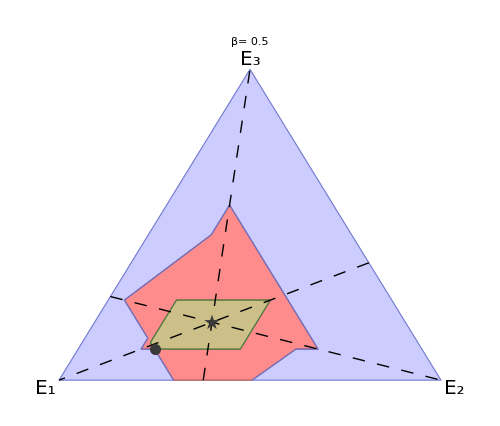

```mathematica
ThermalCones[p,Es,0.5]
```

The algorithm also works for a four-level system:

```mathematica
q={0.13,0.09,0.36,0.42};
```

```mathematica
ThermalCones[q,{0,1,2,4},0.5]
```

-Graphics3D-

Visualizing the evolution of the thermal cones by going from β = 0 to β → ∞:

```mathematica
Monitor[ListAnimate[Table[ThermalConesQuickPlot2D[p,{0,1,2},β],{β,0,4,0.02}]],β]
```

To obtain the past and future thermal cones and the incomparable region separately, one can use the following codes:

Code: PastThermalCone[state, energies, β,], IncomparableRegion[state, energies, β,] and FutureThermalCone[state, energies, β,]

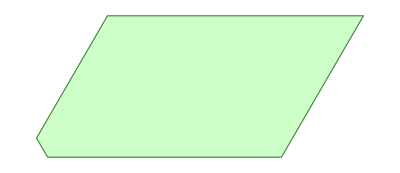

```mathematica
FutureThermalCone[p,Es,β]
```

```mathematica
FutureThermalCone[q,{0,1,2,3},β]
```

-Graphics3D-

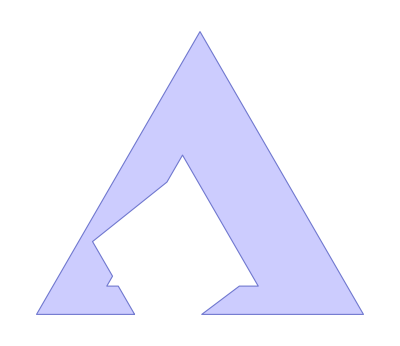

```mathematica
PastThermalCone[p,Es,β]
```

For a four-level system these plots are difficult to visualise due to their inner structure. In order to make their visualisation better, we add a way of controlling their opacity:  PastThermalCone[state, energies, β, opacity], IncomparableRegion[state, energies, β,opacity]

```mathematica
Table[PastThermalCone[q,{0,1,2,3},0,op],{op,{0,0.1,0.5,1}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

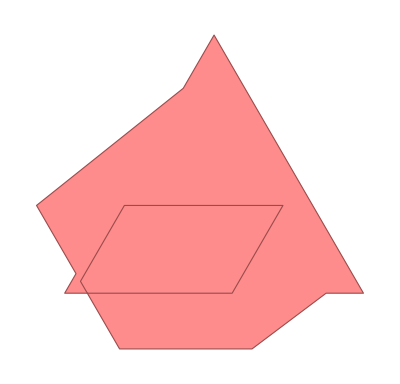

```mathematica
IncomparableThermalRegion[p,Es,β]
```

```mathematica
Table[IncomparableThermalRegion[q,{0,1,2,3},0,op],{op,{0,.1,.5,1}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

To visualise them in each Weyl Chamber, we simply need to use the code: ThermalConesChambers[state, energies, β, chamber]

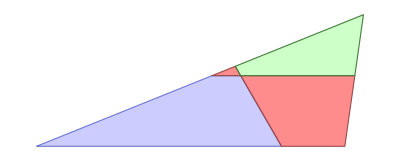

```mathematica
ThermalConesChambers[p,Es,β,6]
```

```mathematica
ThermalConesChambers[q,{0,1,2,3},0,1]
```

-Graphics3D-

To see them separately in each Weyl chamber, we use PastThermalConeChambers[state, energies, β, chamber], IncomparableThermalRegionChambers[state, energies, β, chamber] and FutureThermalConeChambers[state, energies, β, chamber]

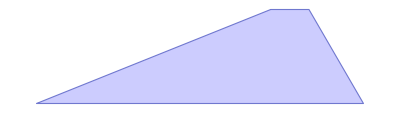

```mathematica
PastThermalConeChambers[p,Es,β,6]
```

```mathematica
PastThermalConeChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

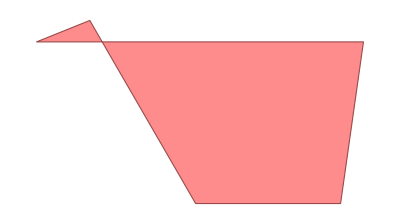

```mathematica
IncomparableThermalRegionChambers[p,Es,β,6]
```

```mathematica
IncomparableThermalRegionChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

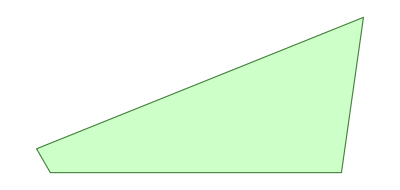

```mathematica
FutureThermalConeChambers[p,Es,β,6]
```

```mathematica
FutureThermalConeChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

These functions are enough to play around with thermal cones and understand their main behaviour.

## Extreme points for arbitrary dimension

For a d-dimensional energy-incoherent state, the set of extreme points of the future and past can be obtained by using the following:

Code: FutureExtremePoints[state, energies, β,],  tvectors[state, energies, β, chamber]

## Example of usage:

For a 7-dimensional state:

```mathematica
test = Normalize[RandomReal[1,7],Total];
```

```mathematica
FutureExtremePoints[test,Range[7],0.5]
```

```mathematica
tvectors[test,Range[7],0.5]
```

## Volumes evolution with β

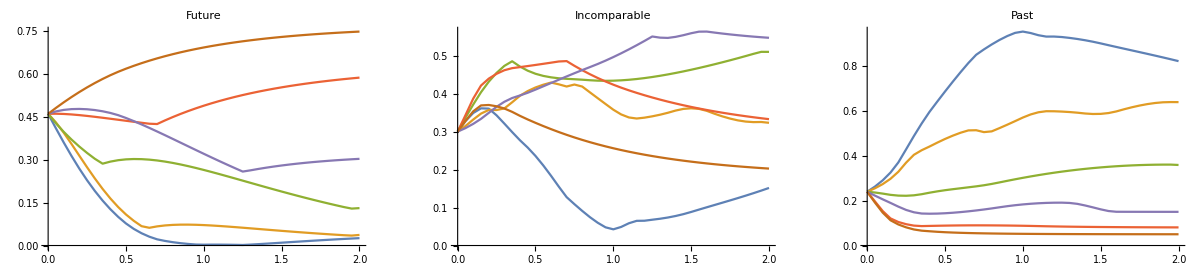

```mathematica
volumesβDependencePlots[{.7,.2,.1},{0,1,2},.05]
```

## Equi-volumetric level sets in dimension 3

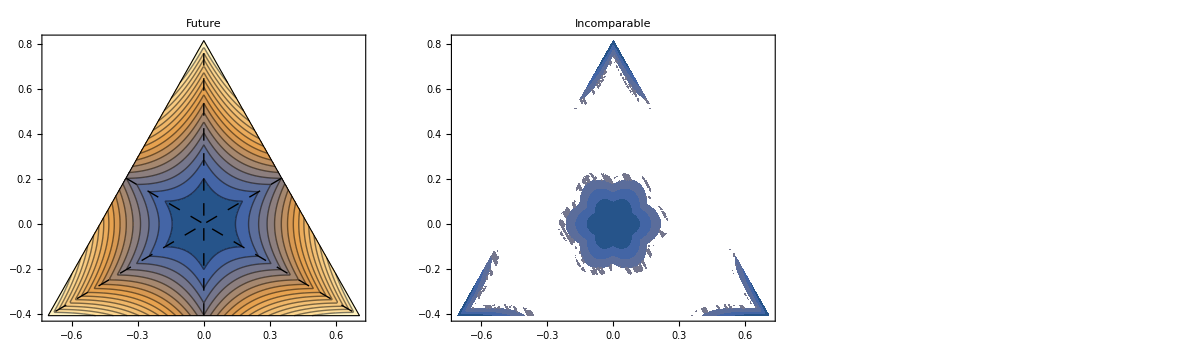

```mathematica
EquivolumetricLinesPlots[0,{0,1,2},.005]
```

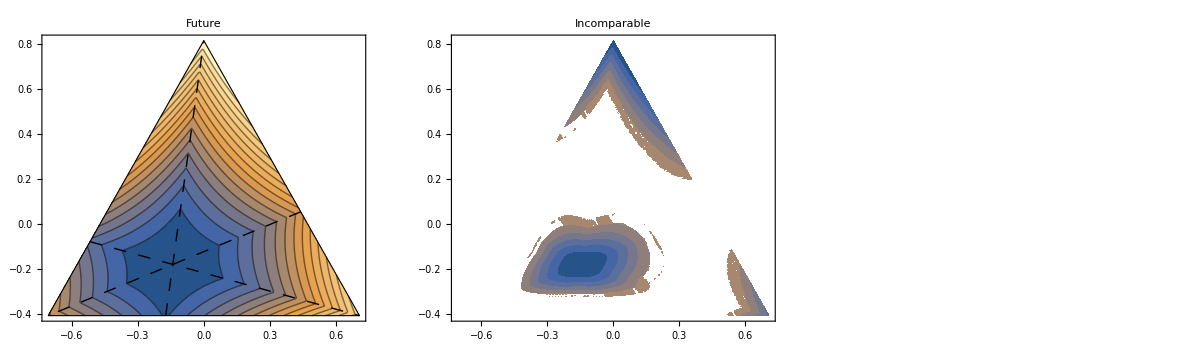

```mathematica
EquivolumetricLinesPlots[0.5,{0,1,2},.005]
```